```mathematica
WeatherDashboard[location_]:=
Framed[
Grid[{{ Text[Style[CommonName[location],Large, Gray]], SpanFromLeft},
{
Show[IconData["AirTemperature",WeatherData[location,"Temperature"]],ImageSize->150],Show[IconData["WindDirection",WeatherData[location, "WindDirection"]],ImageSize->170]},{Show[IconData["RelativeHumidity",WeatherData[location,"Humidity"]],ImageSize->150],Show[IconData["WindSpeed",WeatherData[location,"WindSpeed"]],ImageSize->170]}}],
RoundingRadius->40,FrameMargins->20,FrameStyle->{Thick, Gray}]
```

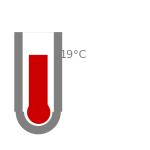
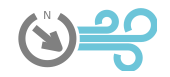
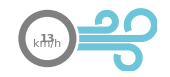
Cairo | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
WeatherDashboard[Entity["City",{"Cairo","Cairo","Egypt"}]]
```

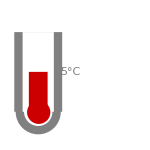
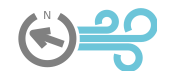
London | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
WeatherDashboard[$GeoLocationCity]
```